```mathematica
(* Notation:
y1=x11*w1+x12*w2;
So xa1 : first component of stimulus A *)
```

```mathematica
findfp[ϕ_,u_]:=(
x11 = Cos[ϕ];
x12 = Sin[ϕ];
x21 = Sin[ϕ];
x22= Cos[ϕ];

w2=w2x/.Solve[(w1+u)*x11/((w2x+u)*x12)==x21/x22,w2x][[1]]; 
y1=x11*w1+x12*w2;
y2=x21*w1+x22*w2;
th=(y1^2+y2^2)/2;
dw = (w1 + u)*x11*y1*(y1- th) + x21*y2*(y2 - th);
S = NSolve[{dw==0 ,(y1-th) <= 0, (y2-th) >= 0},w1,Reals];
numsol = Length[S];
w1= w1/.S[[1]];
w11 = If[numsol == 1, w1, -2];
w12 = If[numsol == 1, w2, -2];
Clear[w1, w2, y1, y2, th, dw];


w2=w2x/.Solve[x11/x12 ==(w1+u)*x21/((w2x+u)*x22),w2x][[1]]; 
y1=x11*w1+x12*w2;
y2=x21*w1+x22*w2;
th=(y1^2+y2^2)/2;
dw = x11*y1*(y1- th) + (w1+ u)*x21*y2*(y2 - th);
S = NSolve[{dw==0,(y2-th) <= 0, (y1 - th) >= 0},w1,Reals];
numsol = Length[S];
w1= w1/.S[[1]];
w21 = If[numsol == 1, w1, -2];
w22 =  If[numsol == 1, w2, -2];
Clear[w1, w2, y1, y2, th, dw];

output = {w11, w12, w21, w22};

Return[output];

)
```

```mathematica
y1f[w1_, w2_, ϕ_] := w1*Cos[ϕ] + w2*Sin[ϕ];
y2f[w1_, w2_, ϕ_] := w1*Sin[ϕ] + w2*Cos[ϕ];
w1f[y1_, y2_, ϕ_] :=( Inverse[{{Cos[ϕ], Sin[ϕ]}, {Sin[ϕ], Cos[ϕ]}}].{y1 , y2})[[1]];
w2f[y1_, y2_, ϕ_] :=( Inverse[{{Cos[ϕ], Sin[ϕ]}, {Sin[ϕ], Cos[ϕ]}}].{y1 , y2})[[2]];
thres[y1_, y2_] := (y1^2 + y2^2)/2;
LTDLTD[y1_, y2_] := y1*(y1 - thres[y1, y2]) < 0 && y2*(y2 - thres[y1, y2]) < 0;
LTDLTP[y1_, y2_] := y1*(y1 - thres[y1, y2]) < 0 && y2*(y2 - thres[y1, y2]) >= 0;
LTPLTD[y1_, y2_] := y1*(y1 - thres[y1, y2]) >= 0 && y2*(y2 - thres[y1, y2]) < 0;
LTPLTP[y1_, y2_] := y1*(y1 - thres[y1, y2]) >= 0 && y2*(y2 - thres[y1, y2]) >= 0;

z1[y1_, y2_] = y1*(y1-thres[y1,y2]);
z2[y1_, y2_] = y2*(y2-thres[y1,y2]);
dw1[y1_,y2_, ϕ_, u_]=(w1f[y1, y2, ϕ] + u)^Boole[z1[y1,y2]<0]*Cos[ϕ]*z1[y1,y2]+(w1f[y1, y2, ϕ] + u)^Boole[z2[y1,y2]<0]*Sin[ϕ]*z2[y1,y2];
dw2[y1_,y2_, ϕ_, u_]=(w2f[y1, y2, ϕ] + u)^Boole[z1[y1,y2]<0]*Sin[ϕ]*z1[y1,y2]+(w2f[y1, y2, ϕ] + u)^Boole[z2[y1,y2]<0]*Cos[ϕ]*z2[y1,y2];

hardbound[w1_, w2_, u_] := ((w1 < -u) || (w2 < -u));
```

```mathematica
phimin = 0.35;
phimax = 0.45;
phistep = 0.05;
numphi= (phimax - phimin)/phistep + 1 ;

umin = -3;
umax = 3;
ustep = 0.05;
numu = (umax - umin)/ustep + 1;

totalpoints = numu*numphi;

Dictable = Table[Subscript[dic,i,j],{i, totalpoints},{j,2}];
FP2A =  Table[Subscript[fp2a,i,j],{i, totalpoints},{j,3}];
FP2B =  Table[Subscript[fp2b,i,j],{i, totalpoints},{j,3}];

iteration = 1;

Do[
Dictable[[iteration]]= {phi,u};
{wa1, wa2, wb1, wb2} = findfp[phi, u];
FP2A[[iteration]] = {phi, u, {wa1, wa2}};
FP2B[[iteration]] = {phi, u, {wb1, wb2}};
iteration++;
, {u,umin,umax,ustep}, {phi,phimin,phimax,phistep}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of w1/.{}⟦1⟧.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of w1/.{}⟦1⟧.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of w1/.{}⟦1⟧.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

```mathematica
w2linfun[w1_,u_,ϕ_]:=(
x11 = Cos[ϕ];
x12 = Sin[ϕ];
x21 = Sin[ϕ];
x22= Cos[ϕ];
w2sola=w2x/.Solve[x11/x12 ==(w1+u)*x21/((w2x+u)*x22),w2x][[1]];
w2solb=w2x/.Solve[x21/x22 ==(w1+u)*x11/((w2x+u)*x12),w2x][[1]];
{w2sola,w2solb})
```

```mathematica
w2linfun[1,1,3/10]
```

{-1+2 Tan[3/10]^2,-1+2 Cot[3/10]^2}

```mathematica
qBCMa[ϕ_,u_]:=(
Pos= Position[SetAccuracy[Dictable, 3], {SetAccuracy[ϕ, 3],SetAccuracy[ u, 3]}];
Return[{FP2A[[Pos[[1, 1]]]][[3,1]],FP2A[[Pos[[1, 1]]]][[3,2]]}]
);

qBCMb[ϕ_,u_]:=(
Pos= Position[SetAccuracy[Dictable, 4], {SetAccuracy[ϕ, 4],SetAccuracy[ u, 4]}];
Return[{FP2B[[Pos[[1, 1]]]][[3,1]],FP2B[[Pos[[1, 1]]]][[3,2]]}]
);
```

```mathematica
makefigure[ϕ_, u_, wmin_, wmax_]:=( 
phasew = RegionPlot[{LTDLTD[y1f[w1, w2, ϕ], y2f[w1, w2, ϕ]], LTDLTP[y1f[w1, w2, ϕ], y2f[w1, w2, ϕ]], LTPLTD[y1f[w1, w2, ϕ], y2f[w1, w2, ϕ]], LTPLTP[y1f[w1, w2, ϕ], y2f[w1, w2, ϕ]]} ,{w1,wmin,wmax},{w2,wmin,wmax},
FrameLabel->{Style[Subscript[w, 1], 16, Black], Style[Subscript[w, 2], 16, Black]},
Epilog->{PointSize[0.03], 
Directive[{Thick,Blue,Dashed}],InfiniteLine[{{-u,-1},{-u,3}}],
(*InfiniteLine[{{-1,-u},{3,-u}}], *)
Directive[{Thick,Blue,Dashed}],
Point[{-u, -u}],
Directive[{Thick,Black,Dashed}],
Point[qBCMa[ϕ, u]],
Point[qBCMb[ϕ, u]],
Directive[{Thick,Red, Dashing[None]}],
Point[{w1f[2, 0, ϕ], w2f[2, 0, ϕ]}],
Point[{w1f[0,2, ϕ], w2f[0, 2, ϕ]}],
Circle[{w1f[0, 0, ϕ], w2f[0, 0, ϕ]}, 0.05],
Circle[{w1f[1,1, ϕ], w2f[1, 1, ϕ]}, 0.05]
},
MaxRecursion->7
];

wshadow1 = RegionPlot[{hardbound[w1, w2, u]}, {w1, wmin, wmax}, {w2, wmin, wmax}, PlotStyle->{Gray}];
(* wshadow define unaccessible regions *)

sp=StreamPlot[{dw1[y1f[w1,w2, ϕ],y2f[w1,w2, ϕ], ϕ, u],dw2[y1f[w1,w2, ϕ],y2f[w1,w2, ϕ], ϕ, u]},{w1,wmin,wmax},{w2,wmin,wmax},
PerformanceGoal:>Quality, StreamStyle->GrayLevel[0.4], StreamPoints->20,StreamScale->Medium];
cp=ContourPlot[{dw1[y1f[w1,w2, ϕ],y2f[w1,w2, ϕ], ϕ, u]==0,dw2[y1f[w1,w2, ϕ],y2f[w1,w2, ϕ], ϕ, u]==0},{w1,wmin,wmax},{w2,wmin,wmax}, PlotPoints->280,PerformanceGoal->Quality];
linep=Plot[w2linfun[w1,u, ϕ],{w1,wmin,wmax}]; (* mvr addition *)

g =GraphicsRow[{
Show[phasew, wshadow1, cp, sp, linep]
(*Show[cp],
Show[ sp, linep]*)
}];
f = Framed[Column[{Style[StringJoin[{"ϕ = ", ToString[ϕ], ", u = ", ToString[u]}] ,14],g},Alignment->Center],FrameMargins->10, FrameStyle->Directive[Thickness@0]];
Return[f]
);
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

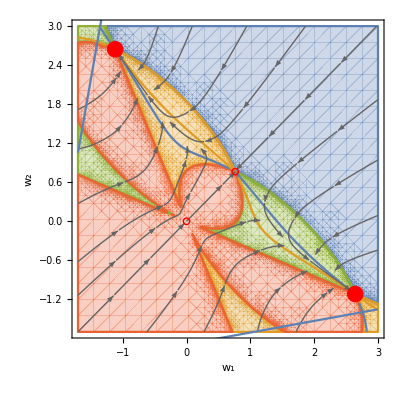
ϕ = 0.4, u = 2.3
-Graphics-

```mathematica
f = makefigure[0.4, 2.3, -1.7, 3]
Export["phase_04_23.pdf",f];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

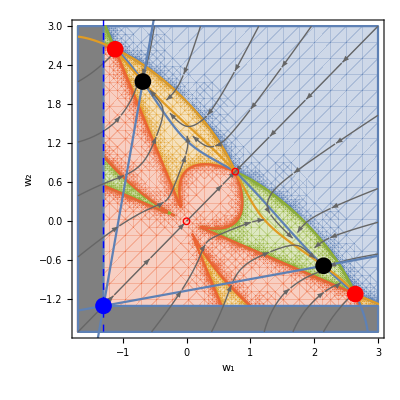
ϕ = 0.4, u = 1.3
-Graphics-

```mathematica
f = makefigure[0.4, 1.3, -1.7, 3]
Export["phase_04_13.pdf",f];
```

```mathematica
f = makefigure[0.4, -0.9, -1.7, 3]
Export["phase_04_m09.pdf",f];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

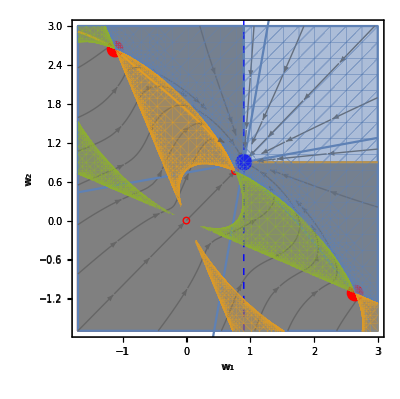
```mathematica
{{"ϕ = 0.4, u = -0.9"}, {-Graphics-}}
```

```mathematica
makefigurezoom[ϕ_, u_, wmin1_, wmax1_,wmin2_, wmax2_]:=( 
phasew = RegionPlot[{LTDLTD[y1f[w1, w2, ϕ], y2f[w1, w2, ϕ]], LTDLTP[y1f[w1, w2, ϕ], y2f[w1, w2, ϕ]], LTPLTD[y1f[w1, w2, ϕ], y2f[w1, w2, ϕ]], LTPLTP[y1f[w1, w2, ϕ], y2f[w1, w2, ϕ]]} ,{w1,wmin1,wmax1},{w2,wmin2,wmax2},
FrameLabel->{Style[Subscript[w, 1], 16, Black], Style[Subscript[w, 2], 16, Black]},
Epilog->{PointSize[0.03], 
Directive[{Thick,Blue,Dashed}],InfiniteLine[{{-u,-1},{-u,3}}],
(*InfiniteLine[{{-1,-u},{3,-u}}], *)
Directive[{Thick,Blue,Dashed}],
Point[{-u, -u}],
Directive[{Thick,Black,Dashed}],
Point[qBCMa[ϕ, u]],
Point[qBCMb[ϕ, u]],
Directive[{Thick,Red, Dashing[None]}],
Point[{w1f[2, 0, ϕ], w2f[2, 0, ϕ]}],
Point[{w1f[0,2, ϕ], w2f[0, 2, ϕ]}],
Circle[{w1f[0, 0, ϕ], w2f[0, 0, ϕ]}, 0.05],
Circle[{w1f[1,1, ϕ], w2f[1, 1, ϕ]}, 0.05]
},
MaxRecursion->7
];

wshadow1 = RegionPlot[{hardbound[w1, w2, u]}, {w1, wmin1, wmax1}, {w2, wmin2, wmax2}, PlotStyle->{Gray}];
(* wshadow define unaccessible regions *)

sp=StreamPlot[{dw1[y1f[w1,w2, ϕ],y2f[w1,w2, ϕ], ϕ, u],dw2[y1f[w1,w2, ϕ],y2f[w1,w2, ϕ], ϕ, u]},{w1,wmin1,wmax1},{w2,wmin2,wmax2},
PerformanceGoal:>Quality, StreamStyle->GrayLevel[0.4], StreamPoints->20,StreamScale->Medium];
cp=ContourPlot[{dw1[y1f[w1,w2, ϕ],y2f[w1,w2, ϕ], ϕ, u]==0,dw2[y1f[w1,w2, ϕ],y2f[w1,w2, ϕ], ϕ, u]==0},{w1,wmin1,wmax1},{w2,wmin2,wmax2}, PlotPoints->280,PerformanceGoal->Quality];
linep=Plot[w2linfun[w1,u, ϕ],{w1,wmin1,wmax1}]; (* mvr addition *)

g =GraphicsRow[{
Show[phasew, wshadow1, cp, sp, linep]
(*Show[cp],
Show[ sp, linep]*)
}];
f = Framed[Column[{Style[StringJoin[{"ϕ = ", ToString[ϕ], ", u = ", ToString[u]}] ,14],g},Alignment->Center],FrameMargins->10, FrameStyle->Directive[Thickness@0]];
Return[f]
);
```

Power::indet: Indeterminate expression 0.^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

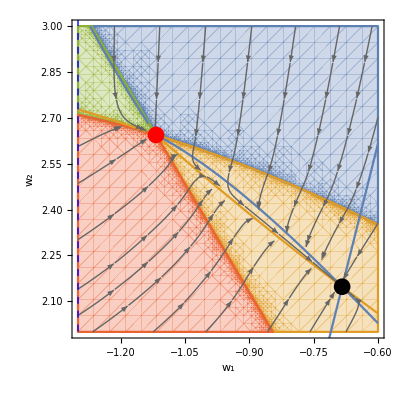
ϕ = 0.4, u = 1.3
-Graphics-

```mathematica
f = makefigurezoom[0.4, 1.3, -1.3, -0.6,2,3]
```